## Traffic Light Problem

```mathematica
ClearAll["Global`*"]
t0 =.;te=.;
x0=.; xe=.; v0=.; ve=.;
c1=.;c2=.;c3=.;c4=.;

SetDirectory[NotebookDirectory[]];
SetOptions[{Plot,ListPlot},PlotStyle->{Thickness[0.006]},
FrameStyle->Directive[Bold],
Frame->{{True,False},{True,False}},
BaseStyle->{FontFamily->"Times",FontSize->38},
PlotRangePadding->0,
GridLines-> Automatic];

lamda1[t_] := c1;
lamda2[t_] := -c1*t-c2;
a[t_] := c1*t+c2;
v[t_] := (1.0/2.0)*c1*t^2 + c2*t + c3;
x[t_] := (1.0/6.0)*c1*t^3 + (1.0/2.0)*c2*t^2 + c3*t + c4; 

c = Solve[{v[t0] == v0, v[te] == ve, x[t0] == x0, x[te] == xe}, {c1,c2,c3,c4}];
c1 = c1/.c[[1]];c2 = c2/.c[[1]];c3 = c3/.c[[1]];c4 = c4/.c[[1]];

cost[te_]=Integrate[0.5*a[t]^2,{t,t0,te}]+0.5*w*te;
Hte=0.5*a[te]^2+lamda1[te]*v[te]+lamda2[te]*a[te]+0.5*w;
CForm[Hte]

t0=0; w =0.1;
v0=8;ve=11;
x0 = 134.5;xe = 220;

tf=NSolve[Hte==0 && te>0,te,Reals]
te=te/.tf[[1]];

costU = Integrate[0.5*a[t]^2,{t,t0,te}]
cost[te]
p1=GraphicsRow[
{Plot[a[t],{t,t0,te},FrameLabel->{{"a (in m/s/s)",None},{"t (in s)", None}},PlotRange->{{0,te},{-.5,.5}},PlotStyle->{Thickness[0.006]}],
Plot[v[t],{t,t0,te},FrameLabel->{{"v (in m/s)",None},{"t (in s)", None}},PlotRange->{{0,te},{0, Max[v0,ve]+5}},FrameTicks-> {{Range[5,Max[v0,ve] +5,5], Automatic}, {Automatic,Automatic}},PlotStyle->{Thickness[0.006]}],
Plot[x[t],{t,t0,te},FrameLabel->{{"x (in m)",None},{"t (in s)", None}},PlotRange->{{0,te},{x0,xe+10}},FrameTicks-> {{Range[50,xe +50,50], Automatic}, {Automatic,Automatic}},PlotStyle->{Thickness[0.006]}]},
 ImageSize->2000];

te=.;
v0=11;ve=5;
tf=NSolve[Hte==0 && te>0,te,Reals];
te=te/.tf[[1]];

costU = Integrate[0.5*a[t]^2,{t,t0,te}];
cost[te];
p2=GraphicsRow[
{Plot[a[t],{t,t0,te},FrameLabel->{{"a (in m/s/s)",None},{"t (in s)", None}},PlotRange->{{0,te},{-.5,.5}},PlotStyle->{Red,Thickness[0.006]}],
Plot[v[t],{t,t0,te},FrameLabel->{{"v (in m/s)",None},{"t (in s)", None}},PlotRange->{{0,te},{0, Max[v0,ve]+5}},FrameTicks-> {{Range[5,Max[v0,ve] +5,5], Automatic}, {Automatic,Automatic}},PlotStyle->{Red,Thickness[0.006]}],
Plot[x[t],{t,t0,te},FrameLabel->{{"x (in m)",None},{"t (in s)", None}},PlotRange->{{0,te},{x0,xe+10}},FrameTicks-> {{Range[50,xe +50,50], Automatic}, {Automatic,Automatic}},PlotStyle->{Red,Thickness[0.006]}]},
 ImageSize->2000];

Show[p1,p2]
```

```mathematica
Red light
```

{{te→38.316}}

38.316

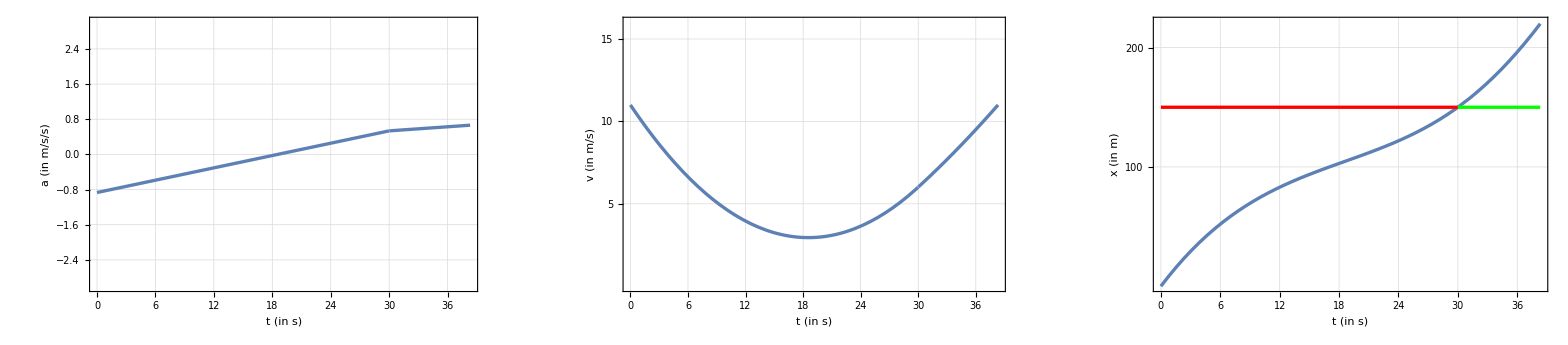

```mathematica
ClearAll["Global`*"]
t0 =.;t1=.;te=.;
x0=.;xred=.; xe=.; v0=.; ve=.;tred=.;
c1=.;c2=.;c3=.;c4=.;c5=.;c6=.;c7=.;c8=.;

f[t_] = Integrate[0.5*a1[t]^2,{t,t0,t1}]+Integrate[0.5*a2[t]^2,{t,t1,te}];

lamda1[t_] = c1;
lamda11[t_]=c5;
lamda2[t_] = -c1*t-c2;
lamda22[t_] = -c5*(t-t1)-c6;
a1[t_] = c1*t+c2;
a2[t_] = c5*(t-t1)+c6;
v1[t_] = (1.0/2.0)*c1*t^2 + c2*t + c3;
v2[t_] = c6*(t-t1) + 0.5*c5*(t-t1)^2+c7;
x1[t_] = (1.0/6.0)*c1*t^3 + (1.0/2.0)*c2*t^2 + c3*t + c4; 
x2[t_] = (1.0/2.0)*c6(t-t1)^2 + (1.0/6.0)*c5*(t-t1)^3+c7*(t-t1)+c8;

cc = Solve[{v1[t0]==v0, v2[te]==ve, x1[t0]==x0, x2[te]==xe, x1[t1]==xred, v1[t1]==v2[t1],x1[t1]==x2[t1], a1[t1]==a2[t1]}, {c1,c2,c3,c4,c5,c6,c7, c8}];
c1 = c1/.cc[[1]];c2 = c2/.cc[[1]];c3 = c3/.cc[[1]];c4 = c4/.cc[[1]];
c5 = c5/.cc[[1]];c6 = c6/.cc[[1]];c7 = c7/.cc[[1]];c8 = c8/.cc[[1]];

Hte=0.5*a2[te]^2+lamda11[te]*v2[te]+lamda22[te]*a2[te]+0.5*w;

(*Initial and Terminal Conditions*)
t0=0; w = 0.1;tred = 30;
v0=11; ve=11;
x0 = 0;xred=150; xe = 220;
t1=30;

tf=NSolve[Hte==0 && te>tred+1,te,Reals]
te=te/.tf[[1]]

costU=Integrate[0.5*a1[t]^2,{t,t0,t1}]+Integrate[0.5*a2[t]^2,{t,t1,te}];
cost=Integrate[0.5*a1[t]^2,{t,t0,t1}]+Integrate[0.5*a2[t]^2,{t,t1,te}]+0.5*w*te;

a[t_]=Piecewise[{{a1[t], t0≤ t≤ t1}, {a2[t], t1≤ t ≤ te}}];
v[t_]=Piecewise[{{v1[t], t0≤ t≤ t1}, {v2[t], t1≤ t ≤ te}}];
x[t_]=Piecewise[{{x1[t], t0≤ t≤ t1}, {x2[t], t1≤  t ≤ te}}];

p11=GraphicsRow[
{Plot[a[t],{t,t0,te},FrameLabel->{{"a (in m/s/s)",None},{"t (in s)", None}},PlotRange->{{0,te},{-3,3}}],
Plot[v[t],{t,t0,te},FrameLabel->{{"v (in m/s)",None},{"t (in s)", None}},PlotRange->{{0,te},{0, Max[v0,ve]+5}},FrameTicks-> {{Range[0+5,Max[v0,ve] +5,5], Automatic}, {Automatic,{0,15}}}],
Show[Plot[x[t],{t,t0,te},FrameLabel->{{"x (in m)",None},{"t (in s)", None}},PlotRange->{{0,te},{0,xe+1}},FrameTicks-> {{Range[x0+100,xe +100,100], Automatic}, {Automatic,Automatic}}],Plot[150,{t,t0,tred},PlotStyle->{Red,Thickness[0.006]}],Plot[150,{t,tred,te},PlotStyle->{Green,Thickness[0.006]}]]},
 ImageSize->2000]

Table[a[t],{t,0,30}];
Table[v[t],{t,0,30}];
Table[x[t],{t,0,30}];

(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~ UP Problem ~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)
t0 =.;te=.; w=.;
x0=.; xe=.; v0=.; ve=.;
c1=.;c2=.;c3=.;c4=.;

lamda1[t_] := c1;
lamda2[t_] := -c1*t-c2;
a[t_] := c1*t+c2;
v[t_] := 1/2*c1*t^2 + c2*t + c3;
x[t_] := 1/6*c1*t^3 + 1/2*c2*t^2 + c3*t + c4; 

c = Solve[{v[t0] == v0, v[te] == ve, x[t0] == x0, x[te] == xe}, {c1,c2,c3,c4}];
c1 = c1/.c[[1]];c2 = c2/.c[[1]];c3 = c3/.c[[1]];c4 = c4/.c[[1]];

Hte=0.5*a[te]^2+lamda1[te]*v[te]+lamda2[te]*a[te]+0.5*w;

te=.;
t0=0; w=0.1;
v0=10; ve=11; 
x0 = 80; xe = 220;
tf=NSolve[Hte==0 && te>0,te,Reals];
te=te/.tf[[1]];

costU=Integrate[0.5*a[t]^2,{t,t0,te}];
cost=Integrate[0.5*a[t]^2,{t,t0,te}]+0.5*w*te;

p22=GraphicsRow[
{Plot[a[t],{t,t0,te},FrameLabel->{{"a (in m/s/s)",None},{"t (in s)", None}},PlotRange->{{0,te},{-3,3}},PlotStyle->{Thickness[0.006],Red,Dashed}],
Plot[v[t],{t,t0,te},FrameLabel->{{"v (in m/s)",None},{"t (in s)", None}},PlotRange->{{0,te},{0, Max[v0,ve]+5}},FrameTicks-> {{Range[0+5,Max[v0,ve] +5,5], Automatic}, {Automatic,Automatic}},PlotStyle->{Thickness[0.006],Red,Dashed}],
Show[Plot[x[t],{t,t0,te},FrameLabel->{{"x (in m)",None},{"t (in s)", None}},PlotRange->{{0,te},{0,xe+1}},FrameTicks-> {{Range[x0+50,xe +50,50], Automatic}, {Automatic,Automatic}},PlotStyle->{Thickness[0.006],Red,Dashed}],Plot[150,{t,t0,tred},PlotStyle->{Red,Thickness[0.006]}],Plot[150,{t,tred,29.9135},PlotStyle->{Green,Thickness[0.006]}]]
},
 ImageSize->2000];
```